```mathematica
f[x_]:=Sum[a[i]x^i,{i,0,2}]
```

```mathematica
CoefficientList[2f[b]-c f[2 b],b]
```

{2 a[0]-c a[0],2 a[1]-2 c a[1],2 a[2]-4 c a[2]}

```mathematica
Plot3D[x y,{x,-4,4},{y,x-4,x+4}]
```

-Graphics3D-

```mathematica
f[a_,b_]:=a^2+b^2;
```

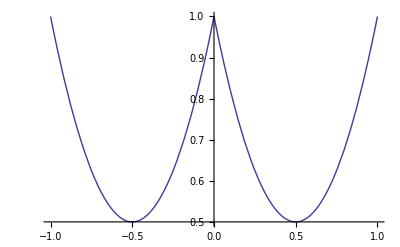

```mathematica
Plot[Max[f[a,1-Abs[a]],f[a,Abs[a]-1]],{a,-1,1}]
```